# Geometric groups

Evaluate this stuff

### basic operations

```mathematica
Off[General::"spell1"]
```

Here is a handy method of building groups and other kinds of lists of useful things

```mathematica
a_⊙b_:=Join @@ Outer[Dot,a,b,1]    (*generates all dot products of elts of a,b*)
x_⊙y_⊙z_:=x⊙(y⊙z)
```

```mathematica
f_⊗g_:=(f⊙{#})& /@ g;                          (*applies g to object f*)

f_⋆A_:=Map[f,A,{2}];                          


f_⊕v_:=Map[#+v&,f,{2}]


Subscript[A_, n_]:=Table[MatrixPower[A,k],{k,0,n-1}]
```

```mathematica
A_⋄B_:=Inverse[B].A.B

A_⋄B_⋄C_:=(A⋄B)⋄C
```

### specific transforms

```mathematica
rot[t_]:=({{Cos[t], Sin[t], 0}, {-Sin[t], Cos[t], 0}, {0, 0, 1}})
trans[{x_,y_}]:=({{1, 0, 0}, {0, 1, 0}, {x, y, 1}})
refx=({{-1, 0, 0}, {0, 1, 0}, {0, 0, 1}});

ident=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
scale[s_]:=scale[s]=({{s, 0, 0}, {0, s, 0}, {0, 0, 1}})
scale[{sx_,sy_}]:=({{sx, 0, 0}, {0, sy, 0}, {0, 0, 1}});
refy=rot[-Pi/2].refx.rot[Pi/2];
```

```mathematica
r3=	Subscript[(rot[2π/3]), 3];
r6 =Subscript[(rot[2π/6]), 6];
```

### moving among models:

```mathematica
homo2cart[vect_]:=Drop[vect,-1]/vect⟦-1⟧

cart2homo[vect_]:=Append[vect,1]

stereo[vect_]:=Drop[vect,-1]/(-vect[[-1]]+1)
stereo2sphere[vect_]:=If[vect.vect>1,
		Append[#,Sqrt[1-#.#]]&[2vect/(vect.vect+1)],
		Append[#,-Sqrt[1-#.#]]&[2vect/(vect.vect+1)]]

Flatproj[vect_]:=Drop[vect,-1]
```

```mathematica
SuperPlus[v_]:=cart2homo[v];
SubPlus[v_]:=homo2cart[v];
```

### helpful graphics stuff

#### miscellaneous

```mathematica
spline[x0_,x1_,v0_,v1_]:=
	a t^3+b t^2 + c t + d/.
		{a->-v1+v0-2x1+2x0,
			b->3x1-3x0-2v0+v1,
			c->v0,d->x0}
```

```mathematica
‖v_‖:=√(v.v)
```

```mathematica
OverBar[v_]:=v/‖v‖//N
```

#### spherical polygon routines

abovelist returns f applied to the components (of length >2) of poly that lie in the positive view direction.  That is, we check which points of poly have poly.view >0.
view can be seen as an axis of projection (say for spherical plots) or as a sided homogeneous line (for poly in homo coords).

```mathematica
abovelist[poly_,view_,f_]:=
	Module[{i,current,dp,pp},
		i=1;
		current={};
		dp=#.view&/@ poly;
	Which[
		And @@ (# <0 & /@ dp), {},
		And @@ (# >0 & /@ dp) && Length[poly]>2,{f[poly]},
		And @@ (# >0 & /@ dp) && Length[poly]<3,{},
     dp⟦1⟧>0,abovelist[RotateLeft[poly],view,f],
			True,
While[dp⟦i⟧<=0, i++];pp=f[poly];
While[dp⟦i⟧>=0 && i< Length[poly],
			current=Append[current,pp⟦i⟧];i++];
Which[
			i==Length[poly] && dp⟦i⟧>=0 && Length[current]>1,{Append[current,pp⟦i⟧]},
			i==Length[poly] && Length[current]>2,{current},
			i==Length[poly], Return[{}],
			Length[current]>2,
			        Append[abovelist[Drop[poly,i],view,f],current],
			True,abovelist[Drop[poly,i-1],view,f]]]];
```

```mathematica
re2co[v_]:=v⟦1⟧+I v⟦2⟧
```

```mathematica
fillin[v1_,v2_,res_]:=Module[{},
		t1=Arg[re2co[v1]];
		t2=Arg[re2co[v2]];
		nn=Abs[t1-t2];
		Which[
			nn>Pi &&t1<t2, t1=t1+2Pi,
			nn>Pi  &&t1>t2, t2=t2+2Pi];
		nnn=Abs[Ceiling[(t1-t2)/res]];
		Which[nnn==0,{},True,
		nnnn=(t2-t1)/nnn;
		
		Table[{Cos[t1+nnnn k],Sin[t1+nnnn k]}//N,{k,1,nnn-1}]//N]]
```

```mathematica
FlatSpherePoly[poly_,view_,bi_,res_]:=
	Join[#,fillin[#⟦-1⟧,#⟦1⟧,res]]& /@ abovelist[poly,view,#.Transpose[{bi,view×bi}]&]
```

```mathematica
st[a_,b_,c_]:=Show[Graphics[Join[
		
			Join @@
					({Hue[.1],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
										ppp
									))
					),	
				
				{GrayLevel[.5],Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]]}
			
			
			
			],AspectRatio->Automatic,Axes->False,PlotRange->All]]
```

```mathematica
ppp=((stereo2sphere /@(homo2cart /@#)//Chop[#,10^-5]&)& /@ (ppoly.#& /@ggg));
```

#### homoline stuff

```mathematica
sform[{a_,0,0}]:={1,0,0};
sform[{a_,b_,0}]:={a/b,1,0};
sform[{a_,b_,c_}]:={a/c,b/c,1};
```

(*to take pt transform to line transform*)

```mathematica
SuperDagger[M_]:=Transpose[Inverse[M]]
```

this takes a homoline to the point closest to the origin on the line

```mathematica
SuperStar[{a_,b_,c_}]:={-c a/(a^2+b^2),-c b/(a^2+b^2),1}
```

Calculates the distance from a hline to a hpt

```mathematica
dist2line[hline_,hpt_]:=
	‖hpt.(trans[Drop[SuperStar[hline],-1]])‖
```

And this gives a point closest from hline to hpt

```mathematica
closestpt[hline_,hpt_]:=SuperStar[(hline.Transpose[#])].#&[
		trans[homo2cart[hpt]]]
```

This gives a signed distance; assuming the normal is not normalized. Note what happens if hpt⟦3⟧==0!

```mathematica
signeddist[hline_,hpt_]:=hline.hpt/‖Drop[hline,-1]‖/hpt⟦3⟧
```

In homoline[pt1,pt2], a choice of normal is given by {a,b} (note not scaled!); this normal points left if one is walking from pt1 to pt2.
Also, homoline[x1,x2] has third coord pos iff x1 to x2 clockwise about origin

```mathematica
homoline[{a_,b_},{c_,d_}]:={b-d,-a+c,-b c+a d}
```

```mathematica
homolines[poly_]:= 
	Module[{},
		pp=Append[poly,poly⟦1⟧];
		Table[homoline[pp⟦i⟧,pp⟦i+1⟧],{i,1,Length[poly]}]]
```

```mathematica
dist2line[hline_,hpt_]:=
	‖hpt.(trans[Drop[SuperStar[hline],-1]])‖
```

```mathematica
inhomopoly[homopoly_,homopt_]:=And @@ (
	#>0& /@ (#.homopt& /@ homopoly))
```

```mathematica
drawhomoline[{a_,b_,c_}]:=
	Module[{p,v},
		v={-b,a}/√(a^2+b^2);
		p=-c {a,b}/(a^2+b^2);
		Line[{p+300 v,p-300 v}]]
```

## the wallpaper groups

### Setting up the groups

The names of the wallpaper groups are given in wallpapergps
atr is the "type" of the group: Z is shearable, Y is stretchable, X is only orthogonally transformable.

G is enough of the group to tile a tile
t is gives the side of the tile
fund gives a polygonal fundamental domain
mirlines gives one copy of each mirror line
rotpts gives the rotation pts.   At the moment it is not clear if the dihedral pts need to be included.
S gives a nice matrix to "set the group up"

H gives the subgroup G/D4
outfund  is a list of lines bounding the output fund region in math coords
tout are the max x-y dimensions of the outfund.

```mathematica
wallpapergps={"2222","22*","22x","2*22","*2222","o","xx","x*","**","442","4*2","*442","333","3*3","*333","632","*632"};
```

```mathematica
(Subscript[mirlines, #]={} )&/@ wallpapergps;
(rotpts[2][#]={})& /@ wallpapergps;
(rotpts[3][#]={})& /@ wallpapergps;
(rotpts[4][#]={})& /@ wallpapergps;
(rotpts[6][#]={})& /@ wallpapergps;
```

```mathematica
(Subscript[atr, #]=Z)&/@{"2222","o"};
(Subscript[atr, #]=Y)&/@{"22*","22x","2*22","*2222","xx","x*","**"};
(Subscript[atr, #]=X)&/@{"442","4*2","*442","333","3*3","*333","632","*632"};
```

```mathematica
(Subscript[c, #]="do")&/@ wallpapergps;
```

```mathematica
Subscript[G, "2222"]={ident, rot[Pi]⋄trans[{1,1}]};

Subscript[t, "2222"]={{2,0},{0,2}};
Subscript[fund, "2222"]={{0,0},{2,0},{2,1},{0,1}};

rotpts[2]["2222"]={{0,0},{1,0},{1,1},{0,1}};
```

```mathematica
Subscript[G, "22*"]={ident,trans[-{1,1}].rot[Pi].trans[{1,1}]}⊙{ident,trans[-{2,0}].refx.trans[{2,0}]};

Subscript[t, "22*"]={{4,0},{0,2}};
Subscript[fund, "22*"]={{0,0},{2,0},{2,1},{0,1}};

rotpts[2]["22*"]={{1,0},{1,1}};
Subscript[mirlines, "22*"]={homoline[{2,0},{2,1}]};

rotpts[2]["22*"]={{1,0},{1,1},{3,0},{3,1}};
Subscript[mirlines, "22*"]={homoline[{2,0},{2,1}],homoline[{0,0},{0,1}]};
```

```mathematica
Subscript[G, "22x"]={ident,rot[Pi].trans[{4,2}],trans[-{1,0}].refx.trans[{1,1}],rot[Pi].trans[-{1,0}].refx.trans[{1,1}]};

Subscript[t, "22x"]=Subscript[t, "22*"];
Subscript[fund, "22x"]=Subscript[fund, "2222"];

rotpts[2]["22x"]={{1,0},{1,1}};
rotpts[2]["22x"]={{1,0},{1,1},{3,0},{3,1}};
```

```mathematica
Subscript[G, "2*22"]={ident,rot[Pi]⋄trans[{1,1}]}⊙{ident,refx⋄trans[{2,0}]}⊙{ident,refy⋄trans[{0,2}]};

Subscript[t, "2*22"]={{4,0},{0,4}};
Subscript[fund, "2*22"]=Subscript[fund, "2222"];
Subscript[mirlines, "2*22"]={homoline[{0,0},{2,0}],homoline[{0,0},{0,2}]};

rotpts[2]["2*22"]={{1,1}};
rotpts[2]["2*22"]={{1,1},{3,1},{1,3},{3,3}};
Subscript[mirlines, "2*22"]={homoline[{0,0},{2,0}],homoline[{0,0},{0,2}],homoline[{2,2},{2,0}],homoline[{2,2},{0,2}]};
```

```mathematica
(*alternatively*)
```

```mathematica
Subscript[G, "2*22"]={ident,(refx⋄rot[-Pi/4])}
			⊙
	{ident,(refx⋄rot[Pi/4])⋄trans[{2,0}]};

Subscript[t, "2*22"]={{2,0},{0,2}};
Subscript[tout, "2*22"]={{2,0},{0,1}};
Subscript[fund, "2*22"]={{0,0},{2,0},{1,1}};
Subscript[mirlines, "2*22"]={homoline[{0,0},{2,2}],homoline[{2,0},{0,2}]};
rotpts[2]["2*22"]={{1,0},{0,1}};
```

```mathematica
Subscript[G, "*2222"]={ident,refx⋄trans[{1,0}]}⊙{ident,refy⋄trans[{0,1}]};
Subscript[t, "*2222"]={{2,0},{0,2}};

Subscript[fund, "*2222"]={{0,0},{1,0},{1,1},{0,1}};
Subscript[mirlines, "*2222"]=homolines[{{0,0},{1,0},{1,1},{0,1}}];
```

```mathematica
Subscript[G, "o"]={ident};
Subscript[t, "o"]={{1,0},{0,1}};
Subscript[fund, "o"]={{0,0},{1,0},{1,1},{0,1}};
```

```mathematica
Subscript[G, "xx"]={ident,refx.trans[{1,1}]};
Subscript[t, "xx"]={{1,0},{0,2}};
Subscript[fund, "xx"]={{0,0},{1,0},{1,1},{0,1}};
```

```mathematica
Subscript[G, "x*"]=Subscript[G, "xx"]⊙{ident,refx⋄trans[{1,0}]};
Subscript[t, "x*"]={{2,0},{0,2}};
Subscript[fund, "x*"]={{0,0},{1,0},{1,1},{0,1}};
Subscript[mirlines, "x*"]={homoline[{1,0},{1,1}]};
```

```mathematica
Subscript[G, "**"]={ident,refx.trans[{2,0}]};
Subscript[t, "**"]={{2,0},{0,1}};
Subscript[fund, "**"]={{0,0},{1,0},{1,1},{0,1}};
Subscript[mirlines, "**"]={homoline[{1,0},{1,1}],homoline[{0,1},{0,0}]};
```

```mathematica
Subscript[G, "442"]=Subscript[(rot[Pi/2]⋄trans[{1,1}]), 4];
Subscript[t, "442"]={{2,0},{0,2}};
Subscript[fund, "442"]={{0,0},{1,0},{1,1},{0,1}};
rotpts[4]["442"]={{0,0},{1,1}};
rotpts[2]["442"]={{1,0}};
rotpts[2]["442"]={{1,0},{0,1}};
```

```mathematica
Subscript[G, "4*2"]=trans[-{1,1}].#.trans[{1,1}] & /@ Subscript[(rot[Pi/2]), 4]⊙
		{ident,refx⋄trans[{2,0}]}⊙
		{ident,refy⋄trans[{0,2}]};
Subscript[t, "4*2"]={{4,0},{0,4}};
Subscript[fund, "4*2"]={{0,0},{1,0},{1,1},{0,1}};
Subscript[mirlines, "4*2"]={homoline[{0,0},{1,0}]};
rotpts[4]["4*2"]={{1,1}};
rotpts[4]["4*2"]={{1,1},{3,1},{1,3},{3,3}};
Subscript[mirlines, "4*2"]={homoline[{0,0},{2,0}],homoline[{0,0},{0,2}],homoline[{2,2},{2,0}],homoline[{2,2},{0,2}]};
```

```mathematica
(*alternatively*)
```

```mathematica
Subscript[G, "4*2"]={ident,rot[-Pi/2]⋄trans[{1,0}]}⊙
		{ident,(refx⋄rot[-Pi/4])}
			⊙
	{ident,(refx⋄rot[Pi/4])⋄trans[{2,0}]};
Subscript[t, "4*2"]={{2,0},{0,2}};
Subscript[tout, "4*2"]={{2,0},{0,1}};
Subscript[fund, "4*2"]={{0,0},{1,1},{0,1}};
rotpts[4]["4*2"]={{1,0},{0,1}};
Subscript[mirlines, "4*2"]={homoline[{0,0},{2,2}],homoline[{2,0},{0,2}]};
```

```mathematica
Subscript[G, "*442"]={refx⋄rot[-Pi/4],ident}⊙Subscript[(rot[Pi/2]⋄trans[{1,1}]), 4];
Subscript[t, "*442"]={{2,0},{0,2}};
Subscript[tout, "*442"]={{1,0},{0,1}};
Subscript[fund, "*442"]={{0,0},{1,0},{1,1}};
Subscript[mirlines, "*442"]=Join[homolines[Subscript[fund, "*442"]],homolines[{{0,2},{1,1},{0,1}}]];
```

```mathematica
Subscript[G, "333"]=
	(i=0;tt={{3/2,√3/2},{3/2,-√3/2},{3/2,-√3/2}};	Join @@({#,#.trans[tt⟦++i⟧]}&/@
	Subscript[(rot[2Pi/3]⋄trans[{1/2,√3/2}]), 3]));

Subscript[H, "333"]=Subscript[(rot[2Pi/3]⋄trans[{1/2,√3/2}]), 3];
Subscript[outfund, "333"]={{0,0},{3/2,0},{3/2,√3},{0,√3}};

Subscript[tout, "333"]={{3/2,0},{0,√3}};
			
Subscript[t, "333"]={{3,0},{0,√3}};
Subscript[fund, "333"]={{0,0},{1,0},{3/2,√3/2},{1/2,√3/2}};

rotpts[3]["333"]={{0,0},{1,0},{1/2,√3/2}};

rotpts[3]["333"]={{-1/2,(√3)/2},{0,0},{1/2,(√3)/2},{1,0},{3/2,(√3)/2},{2,0},{5/2,(√3)/2}};
```

```mathematica
Subscript[G, "3*3"]=
		
	(Append[Drop[#,{2}],#⟦2⟧.trans[{-√3,0}]]&[
	(Subscript[(rot[2Pi/3]⋄trans[{√3/2,1/2}]), 3]⊙({ident,refy⋄rot[-Pi/3]⋄trans[{√3,0}]}))])⊙{ident,refy⋄trans[{0,3/2}]};
					
					
		
Subscript[H, "3*3"]=Subscript[(rot[2Pi/3]⋄trans[{√3/2,1/2}]), 3];
Subscript[outfund, "3*3"]={{0,0},{√3,0},{√3/2,3/2}};
	
Subscript[t, "3*3"]={{√3,0},{0,3}};
Subscript[tout, "3*3"]={{√3,0},{0,3/2}};
Subscript[fund, "3*3"]={{0,0},{√3,0},{√3/2,1/2}};
Subscript[mirlines, "3*3"]={homoline[{0,0},{√3,0}]};
rotpts[3]["3*3"]={{√3/2,1/2}};

rotpts[3]["3*3"]={{0,1},{0,2},{(√3)/2,1/2},{(√3)/2,5/2}};
Subscript[mirlines, "3*3"]=Join[homolines[{{0,0},{√3,0},{√3/2,3/2}}],{homoline[{0,3/2},{√3,3/2}]}];
```

```mathematica
Subscript[G, "*333"]=	(i=0;ttt={{3/2,√3/2},{3/2,-√3/2},{0,0}};tt=ttt⟦#⟧&/@{1,2,2,1,2,1};
		Join @@ 
			({#,#.trans[tt⟦++i⟧]}&/@(
		{ident,refy⋄rot[-Pi/3]⋄trans[{1,0}]}⊙Subscript[(rot[2Pi/3]⋄trans[{1/2,√3/2}]), 3])));
Subscript[H, "*333"]=
		{ident,refy⋄rot[-Pi/3]⋄trans[{1,0}],rot[-2Pi/3]⋄trans[{1,0}]};
Subscript[t, "*333"]={{3,0},{0,√3}};
Subscript[tout, "*333"]={{2,0},{0,√3/2}};

Subscript[fund, "*333"]={{0,0},{1,0},{1/2,√3/2}};
Subscript[outfund, "*333"]={{0,0},{2,0},{3/2,√3/2},{1/2,√3/2}};
Subscript[mirlines, "*333"]=homolines[Subscript[fund, "*333"]];

Subscript[mirlines, "*333"]=Join[homolines[Subscript[fund, "*333"]],homolines[#+{3/2,√3/2}&/@ Subscript[fund, "*333"]],
	{homoline[{1,√3},{2,0}],homoline[{2,0},{3,√3}]}];
```

```mathematica
Subscript[G, "632"]=	(i=0;ttt={{3/2,√3/2},{3/2,-√3/2}};tt=ttt⟦#⟧&/@{1,2,2,1,2,1};
		Join @@ 
			({#,#.trans[tt⟦++i⟧]}&/@
					
			(Subscript[(rot[Pi]⋄trans[{3/4,√3/4}]), 2]⊙Subscript[(rot[2Pi/3]⋄trans[{1/2,√3/2}]), 3])));
			
			
Subscript[H, "632"]={ident,rot[Pi]⋄trans[{3/4,√3/4}],rot[-2Pi/3]⋄trans[{1,0}]};

Subscript[tout, "632"]={{1,0},{0,√3}};
		

Subscript[t, "632"]={{3,0},{0,√3}};
Subscript[fund, "632"]={{0,0},{1,0},{1/2,√3/2}};

Subscript[outfund, "632"]={{0,0},{2,0},{3/2,√3/2},{1/2,√3/2}};
rotpts[6]["632"]={{0,0}};
rotpts[3]["632"]={{1/2,√3/2}};
rotpts[2]["632"]={{3/4,√3/4}};

rotpts[2]["632"]=Drop[homo2cart/@(({3/4,(√3)/4,1}.#&/@ Subscript[G, "632"])//Union),{-3}];
rotpts[6]["632"]={{0,0},{3/2,√3/2}};

rotpts[3]["632"]={{-1/2,(√3)/2},{1/2,(√3)/2},{1,0},{2,0},{5/2,(√3)/2}};
```

```mathematica
Subscript[G, "*632"]={ident,rot[Pi/3],refy⋄rot[Pi/6]}⊙({ident,rot[Pi]⋄trans[{3/4,√3/4}]}⊙{ident,refx⋄trans[{3/2,0}]}⊙{ident,refy⋄trans[{0,√3/2}]});
	
	Subscript[H, "*632"]={ident,refy⋄rot[Pi/6],refy⋄rot[Pi/3]};
	
Subscript[t, "*632"]=Subscript[t, "632"];

Subscript[tout, "*632"]=Subscript[tout, "632"];

Subscript[fund, "*632"]={{0,0},{1,0},{3/4,√3/4}};

Subscript[outfund, "*632"]={{0,0},{1,0},{1/2,√3/2},{0,√3/2}};
Subscript[mirlines, "*632"]=homolines[Subscript[fund, "*632"]];

Subscript[mirlines, "*632"]=Drop[Drop[(sform/@(homolines[Subscript[fund, "*632"]]⊙(SuperDagger[#]&/@ Subscript[G, "632"])))//Union,{12}],{10}];
```

```mathematica
(Subscript[S, #]=(ss=#;
	trans[-Plus @@ #/Length[#]&[Subscript[fund, ss]]].{{#,0,0},{0,#,0},{0,0,1}}&[1/Max[#⟦1⟧ &/@ Subscript[fund, #]]/2].trans[{.5,.5}]))&/@  wallpapergps;
```

```mathematica
(Subscript[hpoly, #]=homolines[Subscript[fund, #]])& /@ wallpapergps;
```

```mathematica
(Subscript[mirlines, #]=sform/@Subscript[mirlines, #])&/@wallpapergps;
```

```mathematica
(Subscript[fundims, #]={Max[#⟦1⟧&/@(Subscript[fund, #])],
			Max[#⟦2⟧&/@(Subscript[fund, #])]})&/@ wallpapergps;
```

#### For a number of groups we can derive H, K and outfund immediately:

```mathematica
(Subscript[H, #]={ident};  Subscript[outfund, #]=Subscript[fund, #])&/@{"2222", "22*","22x","*2222","o","**","x*","xx","442","2*22","4*2","*442"};
```

```mathematica
(Subscript[tout, #]=Subscript[t, #])&/@{"2222","22*","22x","*2222","442","o","x*","**","xx"};
```

#### But others take more care and are dealt with above.

### quick illustrations

#### setting things up

```mathematica
fundtest[name_]:=
	
	
	Show[
	Graphics[Join[
				
				
					{Hue[.3],Polygon[Subscript[fund, name]],
				GrayLevel[0],Thickness[.01],Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Hue[.13],EdgeForm[{GrayLevel[0],Thickness[.004]}]},
					
				
					
					Line /@ Map[homo2cart,  (((cart2homo /@ (Subscript[fund, name] // Append[#,#⟦1⟧]&))⊙{#})& /@  
							Subscript[G, name]),{2}],
								
			
				{GrayLevel[0],Text[name,.8{Subscript[t, name]⟦1,1⟧,Subscript[t, name]⟦2,2⟧}],
				Thickness[.005],GrayLevel[.6],Line[{{0,0},Subscript[t, name]⟦2⟧,Plus @@ Subscript[t, name],Subscript[t, name]⟦1⟧,{0,0}}]
				}
				
				
				
				],
	
AspectRatio->Automatic]]
```

```mathematica
ellipse={.2 Sin[t],.6Cos[t],1}.rot[Pi/3].trans[{.5,.5}];
```

```mathematica
ar=((cart2homo/@ {{0,0},{0,1},{.5,1},{.5,.5},{0,.5},{.5,0}})⊙{scale[.6].rot[Pi/6].trans[{.5,.1}]});
```

```mathematica
sswirl[aa_,n_,pts_,gg_]:=(
	cart2homo/@
	Table[

{Sin[n t]Cos[t-aa Sin[n t]],Sin[n t]Sin[t-aa Sin[n t]]},{t,0,Pi/n,Pi/n/pts}]//Chop[#,10^-6]&)
⊙
{gg};
```

```mathematica
swirl=sswirl[7,.8,100,rot[-Pi/6].scale[1.1{.42,.3}].trans[{.4,.4}].scale[1]];
```

```mathematica
test3[name_]:=test3[name,swirl];
```

```mathematica
test3[name_,curve_]:=
	
	(
	
	Show[
	Graphics[Join[
				
				
					{Hue[.3],Polygon[Subscript[fund, name]],
				GrayLevel[0],Thickness[.01],Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Hue[.13],EdgeForm[{GrayLevel[0],Thickness[.004]}]},
					
				
					
					Polygon /@ Map[homo2cart,  ((curve⊙{#})& /@  
							(Subscript[G, name]⊙ 
									Join @@ Table[trans[Subscript[t, name]⟦1⟧ i + Subscript[t, name]⟦2⟧ j],{i,If[name==="3*3"||name==="*632",-1,0],1},{j,If[name==="3*3"||name==="*632",-1,0],1}])),{2}],
		
			
			
				{GrayLevel[0],Text[name,.8{Subscript[t, name]⟦1,1⟧,Subscript[t, name]⟦2,2⟧}],
				Thickness[.005],GrayLevel[.6],Line[{{0,0},Subscript[t, name]⟦2⟧,Plus @@ Subscript[t, name],Subscript[t, name]⟦1⟧,{0,0}}]
				},
					
				
					
					{Hue[1],Thickness[.01]},
					If[!Subscript[mirlines, name]==={},
						drawhomoline /@ Subscript[mirlines, name],{}],
					
					{Hue[.9],PointSize[.05]},
					
				
					If[!(rotpts[2][name]==={}),Point /@ (rotpts[2][name]),{}],
						{Hue[.82]},
					
				
					If[!(rotpts[3][name]==={}),Point /@ (rotpts[3][name]),{}],
						{Hue[.74],PointSize[.05]},
					
				
					If[!(rotpts[4][name]==={}),Point /@ (rotpts[4][name]),{}],
							{Hue[.65],PointSize[.05]},
					
				
					If[!(rotpts[6][name]==={}),Point /@ (rotpts[6][name]),{}]
				
				],
	
AspectRatio->Automatic,PlotRange->{{0-.1,Subscript[t, name]⟦1,1⟧+.1},{0-.1,Subscript[t, name]⟦2,2⟧+.1}}]];
	)
```

```mathematica
test5[name_,curve_]:=
	
	(
	
	Show[
	Graphics[Join[
				
				
					{Hue[.4],Polygon[Subscript[outfund, name]],
				GrayLevel[0],Thickness[.01],Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Hue[.13],EdgeForm[{GrayLevel[0],Thickness[.004]}]},
					
				
					
					Polygon /@ Map[homo2cart,  ((curve⊙{#})& /@  
							(Subscript[H, name]⊙ 
									Join @@ Table[trans[Subscript[t, name]⟦1⟧ i + Subscript[t, name]⟦2⟧ j],{i,If[name==="3*3"||name==="*632",-1,0],0},{j,If[name==="3*3"||name==="*632",-1,0],0}])),{2}],
		
			
			
				{GrayLevel[0],Text[name,.8{Subscript[t, name]⟦1,1⟧,Subscript[t, name]⟦2,2⟧}],
				Thickness[.005],GrayLevel[.6],Line[{{0,0},Subscript[t, name]⟦2⟧,Plus @@ Subscript[t, name],Subscript[t, name]⟦1⟧,{0,0}}]
				},
					
				
					
					{Hue[1],Thickness[.01]},
					If[!Subscript[mirlines, name]==={},
						drawhomoline /@ Subscript[mirlines, name],{}],
					
					{Hue[.9],PointSize[.05]},
					
				
					If[!(rotpts[2][name]==={}),Point /@ (rotpts[2][name]),{}],
						{Hue[.82]},
					
				
					If[!(rotpts[3][name]==={}),Point /@ (rotpts[3][name]),{}],
						{Hue[.74],PointSize[.05]},
					
				
					If[!(rotpts[4][name]==={}),Point /@ (rotpts[4][name]),{}],
							{Hue[.65],PointSize[.05]},
					
				
					If[!(rotpts[6][name]==={}),Point /@ (rotpts[6][name]),{}]
				
				],
	
AspectRatio->Automatic,PlotRange->{{0-.1,Subscript[t, name]⟦1,1⟧+.1},{0-.1,Subscript[t, name]⟦2,2⟧+.1}}]];
	)
```

```mathematica
test4[name_,curve_]:=		Show[
		
		
		
		Graphics[Join[
					
					{GrayLevel[.7]},
					If[!mirbound==={},
						
						drawhomoline /@ ((#.Transpose[Inverse[Subscript[S, name]]])& /@ Subscript[mirbound, name])],{GrayLevel[0]},
					
						{Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],
					
						
					Line[Append[#,#⟦1⟧]& [ (homo2cart /@( (cart2homo /@ Subscript[fund, name] ).Subscript[S, name]))]]}
				
				
				],
					
				AspectRatio->Automatic,PlotRange->{{0,1},{0,1}}]
		
		
		
];
```

```mathematica
test4[name_]:=test4[name,swirl]
```

#### Examples

```mathematica
test3["4*2",swirl]
```

```mathematica
test5 [#,swirl]&/@ wallpapergps
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### writing the groups out

```mathematica
commentQ=False;
```

```mathematica
file="Sally:Desktop Folder:wallpapergps"
```

Sally:Desktop Folder:wallpapergps

```mathematica
file="Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt"
```

Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt

```mathematica
OpenWrite[file]
```

OutputStream[Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt,4]

```mathematica
matwrite[file_,matr_]:=
	(Table[
				WriteString[file,Sequence @@ (Join @@ Table[{ToString[OutputForm[PaddedForm[matr⟦i,j⟧//N,{8,6}]]],"    "},{j,1,3}])];
				
		WriteString[file,"\n"],{i,1,3}];WriteString[file,"\n"])
```

```mathematica
sp="    ";
```

```mathematica
numwrite[n_]:=ToString[OutputForm[PaddedForm[n//N,{8,6}]]]
```

```mathematica
gpwrite[file_,name_]:=
	(WriteString[file,
			
			
			
			If[commentQ,"\n################",""]<>
				
					"\n \n"<> name<>
					"    "<> ToString[Subscript[atr, name]]<>"\n\n"<>
					
					
					If[commentQ,"# bounds of the fund region\n",""]<>
					
					 numwrite[Max[#⟦1⟧&/@(Subscript[fund, name])]]<>sp<>
				numwrite[Max[#⟦2⟧&/@(Subscript[fund, name])]]<>"\n\n"<>
					
					If[commentQ,"# bounds of the tile\n",""]<>
				
				numwrite[Subscript[t, name]⟦1,1⟧] <>sp <>	numwrite[Subscript[t, name]⟦2,2⟧]<>"\n\n"];
		
		WriteString[file,	
				If[commentQ,	"# the fund region\n",""]<>
					ToString[Length[Subscript[fund, name]]]<>"\n"];
					
			Table[WriteString[file,numwrite[Subscript[fund, name]⟦i,1⟧]<>sp<>numwrite[Subscript[fund, name]⟦i,2⟧]<>"\n"],
				{i,1,Length[Subscript[fund, name]]}];WriteString[file,"\n\n"];
		
	 If[commentQ,WriteString[file,"# the mirror lines and rotation points\n"]];			
	
		WriteString[file,ToString[Length[Subscript[mirlines, name]]]<>"\n"];
		i=0; While[i<Length[Subscript[mirlines, name]],i++;
			WriteString[file,numwrite[Subscript[mirlines, name][[i,1]]]<>"   "<>
					numwrite[Subscript[mirlines, name][[i,2]]]<>sp<>numwrite[Subscript[mirlines, name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];
	
				WriteString[file,ToString[Length[rotpts[2][name]]]<>"\n"];
				i=0; While[i<Length[rotpts[2][name]],i++;
			WriteString[file,
					numwrite[rotpts[2][name][[i,1]]]<>sp<>numwrite[rotpts[2][name][[i,2]]]<>"\n"]];
		WriteString[file,"\n"];			
		
			WriteString[file,ToString[Length[rotpts[3][name]]]<>"\n"];
		i=0; While[i<Length[rotpts[3][name]],i++;
			WriteString[file,
					numwrite[rotpts[3][name][[i,1]]]<>sp<>numwrite[rotpts[3][name][[i,2]]]<>"\n"]];
		WriteString[file,"\n"];			
					
			WriteString[file,ToString[Length[rotpts[4][name]]]<>"\n"];
		i=0; While[i<Length[rotpts[4][name]],i++;
			WriteString[file,
					numwrite[rotpts[4][name][[i,1]]]<>sp<>numwrite[rotpts[4][name][[i,2]]]<>"\n"]];
		WriteString[file,"\n"];			
				
				WriteString[file,ToString[Length[rotpts[6][name]]]<>"\n"];	
		i=0; While[i<Length[rotpts[6][name]],i++;
			WriteString[file,
					numwrite[rotpts[6][name][[i,1]]]<>sp<>numwrite[rotpts[6][name][[i,2]]]<>"\n"]];
		
					If[commentQ,WriteString[file,"\n\n# the transforms\n"]];	
				
				WriteString[file,
				"\n"<>ToString[Length[Subscript[G, name]]]<>sp<>
			"\n\n"];
					
					Table[matwrite[file,Subscript[G, name]⟦i⟧],{i,1,Length[Subscript[G, name]]}];
		
		
		WriteString[file,"\n\n"];
		
		(*
		
		If[commentQ,WriteString[file,"# dimensions of output tile\n"]];
		
				WriteString[file,numwrite[Subscript[tout, name]⟦1,1⟧] <>sp <>	numwrite[Subscript[tout, name]⟦2,2⟧]<>"\n\n"];


	WriteString[file,"\n\n"];
		
		If[commentQ,WriteString[file,"# bounding lines of output region\n"]];

		

WriteString[file,
			ToString[Length[Subscript[outfund, name]]]<>"\n"];

			Table[WriteString[file,numwrite[Subscript[outfund, name]⟦i,1⟧]<>sp<>numwrite[Subscript[outfund, name]⟦i,2⟧]<>"\n"],
				{i,1,Length[Subscript[outfund, name]]}];

WriteString[file,"\n\n"];
					


		
					WriteString[file,"\n\n"];
		If[commentQ,WriteString[file,"# transforms needed to build small output tile\n"]];
		
		WriteString[file,
				ToString[Length[Subscript[H, name]]]<>sp<>
			"\n\n"];
					
					Table[matwrite[file,Subscript[H, name]⟦i⟧],{i,1,Length[Subscript[H, name]]}];
		
		WriteString[file,"\n\n\n"];
	
	*)
	
	
	)
```

```mathematica
WriteString[file, "17\n"];

gpwrite[file,#]&/@wallpapergps;Close[file]
```

Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt

### stereo^-1 images

```mathematica
cc=cart2homo /@ Subscript[c, "632"];
```

```mathematica
ss=cart2homo [ (spline@@ (Join[homo2cart /@ {cc⟦2⟧,cc⟦2⟧.rot[Pi/3]},{{-7,-3},{4,-1}}/4]))]//N;
```

```mathematica
ep=.05;
ppoly= (Join @@ (
	(Table[ss,{t,ep,1,ep}])
	
	⊗(r6⊙{scale[.9].rot[ - Pi/20]}//N)//Chop[#,10^-5]&))//Append[#,#⟦1⟧]&;
```

```mathematica
Show[Graphics[Join[{PointSize[.03]},Point[SubPlus[(#)]]&/@ cc,{Line[homo2cart /@ ppoly]}],AspectRatio->Automatic,Axes->True]]
```

⁃Graphics⁃

```mathematica
ggg=((Join @@ Table[trans[SubPlus[(cc⟦3⟧)] 2i+SubPlus[(cc⟦3⟧.rot[2π/3])]  2j+SubPlus[(cc⟦2⟧.rot[π/3])]],{i,0,15},{j,0,15}])⊙r3 //N)⊙{scale[.3]};
```

```mathematica
Show[Graphics[
		
		Polygon[(homo2cart /@#)]& /@ (ppoly⊗ ggg),AspectRatio->Automatic]]
```

⁃Graphics⁃

#### ex

```mathematica
st[1,2,2]
```

## And now the spherical groups

## preparing...

```mathematica
refz=({{1, 0, 0}, {0, 1, 0}, {0, 0, -1}});
rot3=Table[MatrixPower[({{0, 1, 0}, {0, 0, 1}, {1, 0, 0}}),k],{k,0,2}];
rot4=Table[MatrixPower[rot[Pi/2],k],{k,0,3}];

ℐ=ident;

ϕ=(√5+1)/2;τ=(√5-1)/2;
rot5=Table[MatrixPower[({{1, -ϕ, τ}, {ϕ, τ, -1}, {τ, 1, ϕ}})/2,k]//Simplify,{k,0,4}];
```

```mathematica
rotemp[{a_,b_,c_}]:=rotemp[{a,b,c}]= 
		{({{a/(√(a^2+b^2)), -b/(√(a^2+b^2)), 0}, {b/(√(a^2+b^2)), a/(√(a^2+b^2)), 0}, {0, 0, 1}}).({{c/(√(a^2+b^2+c^2)), 0, (√(a^2+b^2))/(√(a^2+b^2+c^2))}, {0, 1, 0}, {-(√(a^2+b^2))/(√(a^2+b^2+c^2)), 0, c/(√(a^2+b^2+c^2))}}),({{c/(√(a^2+b^2+c^2)), 0, -(√(a^2+b^2))/(√(a^2+b^2+c^2))}, {0, 1, 0}, {(√(a^2+b^2))/(√(a^2+b^2+c^2)), 0, c/(√(a^2+b^2+c^2))}}).	({{a/(√(a^2+b^2)), b/(√(a^2+b^2)), 0}, {-b/(√(a^2+b^2)), a/(√(a^2+b^2)), 0}, {0, 0, 1}})}//N
```

```mathematica
rot[{a_,b_,c_},θ_]:=
rotemp[{a,b,c}]⟦1⟧.({{Cos[θ], Sin[θ], 0}, {-Sin[θ], Cos[θ], 0}, {0, 0, 1}}).rotemp[{a,b,c}]⟦2⟧//N
```

```mathematica
rot[{0,0,a_},θ_]:=rotz[θ]
```

```mathematica
rotz[θ_]:=rot[θ]
```

```mathematica
rotx[θ_]:=rotx[θ]=rot3⟦3⟧.rotz[θ].rot3⟦2⟧
```

```mathematica
roty[θ_]:=roty[θ]=rot3⟦2⟧.rotz[θ].rot3⟦3⟧
```

## Groups

```mathematica
Clear[G]
Subscript[G, "222"]={ℐ,refx.refz,refx.refy,refy.refz};
Subscript[G, "*222"]={ℐ,refz}⊙{ℐ,refy}⊙{ℐ,refx};

Subscript[G, "332"]=rot3⊙Subscript[G, "222"];

Subscript[G, "3*2"]=rot3⊙Subscript[G, "*222"];

Subscript[G, "*332"]={ℐ,rotz[Pi/4].refx.rotz[-Pi/4]}⊙Subscript[G, "332"];
Subscript[G, "432"]=rot4⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3;

Subscript[G, "*432"]={ℐ,refx}⊙Subscript[G, "432"];

Subscript[G, "532"]=({ℐ,rot[Pi]}⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3)⊙rot5;

Subscript[G, "*532"]=({ℐ,rot[Pi]}⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3)⊙rot5⊙{ℐ,refx};
Subscript[G, "nn",n_]:=Subscript[G, #<>#&[ToString[n]]]=Subscript[(rot[{0,0,1},2Pi/n]), n]//N;
Subscript[G, "*nn",n_]:=Subscript[G, "*"<>#<>#&[ToString[n]]]=Subscript[G, "nn",n]⊙{ℐ,refx};

Subscript[G, "22n",n_]:=Subscript[G, "22"<>ToString[n]]=Subscript[G, "nn",n]⊙{ℐ,rot[Pi]};


Subscript[G, "nx",n_]:=Subscript[G, ToString[n]<>"x"]=Subscript[G, "nn",n]⊙{ℐ,rotz[π/n].refz}⊙Subscript[G, "nn",n]

Subscript[G, "n*",n_]:=Subscript[G, ToString[n]<>"*"]=Subscript[G, "nn",n]⊙{ℐ,refz}

Subscript[G, "2*n",n_]:=Subscript[G, "2*"<>ToString[n]]=Subscript[G, "*nn",n]⊙{ℐ,rotz[π/n].rotx[π].rotz[-π/n]}

Subscript[G, "*22n",n_]:=Subscript[G, "*22"<>ToString[n]]=Subscript[G, "*nn",n]⊙{ℐ,refz}
```

```mathematica
Clear[G]

G["222"]={ℐ,refx.refz,refx.refy,refy.refz};
G["*222"]={ℐ,refz}⊙{ℐ,refy}⊙{ℐ,refx};

G["332"]=rot3⊙Subscript[G, "222"];

G["3*2"]=rot3⊙Subscript[G, "*222"];

G["*332"]={ℐ,rotz[Pi/4].refx.rotz[-Pi/4]}⊙Subscript[G, "332"];
G["432"]=rot4⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3;

G["*432"]={ℐ,refx}⊙Subscript[G, "432"];

G["532"]=({ℐ,rot[Pi]}⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3)⊙rot5;

G["*532"]=({ℐ,rot[Pi]}⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3)⊙rot5⊙{ℐ,refx};
G["nn"][n_]:=Subscript[G, #<>#&[ToString[n]]]=Subscript[(rot[{0,0,1},2Pi/n]), n]//N;
G["*nn"][n_]:=Subscript[G, "*"<>#<>#&[ToString[n]]]=Subscript[G, "nn",n]⊙{ℐ,refx};

G["22n"][n_]:=Subscript[G, "22"<>ToString[n]]=Subscript[G, "nn",n]⊙{ℐ,rot[Pi]};


G["nx"][n_]:=Subscript[G, ToString[n]<>"x"]=Subscript[G, "nn",n]⊙{ℐ,rotz[π/n].refz}⊙Subscript[G, "nn",n]

G["n*"][n_]:=Subscript[G, ToString[n]<>"*"]=Subscript[G, "nn",n]⊙{ℐ,refz}

G["2*n"][n_]:=Subscript[G, "2*"<>ToString[n]]=Subscript[G, "*nn",n]⊙{ℐ,rotz[π/n].rotx[π].rotz[-π/n]}

G["*22n"][n_]:=Subscript[G, "*22"<>ToString[n]]=Subscript[G, "*nn",n]⊙{ℐ,refz}
```

```mathematica
groups={"222","3*2","*332","432","*432","532","*532"};
ngroups={{"nn",5},{"22n",3},{"*nn",5},{"nx",1},{"n*",4},{"2*n",3},{"*22n",2}};
```

## Tests

```mathematica
curly=Append[#,√(1-#.#)]& /@ Table[.2{t Cos[9 t],t Sin[9 t]}+{.3,.4},{t,0,1,.02}];
```

```mathematica
Show[Graphics3D[Line[curly]]]
```

⁃Graphics3D⁃

```mathematica
mask=ParametricPlot3D[{.99 Cos[u]Sin[v],.99Sin[u]Sin[v],.99Cos[v],{FaceForm[GrayLevel[1]],EdgeForm[]}},
			{u,0,2Pi},{v,0,Pi},Lighting->False,Boxed->False,Axes->False,DisplayFunction->Identity];
```

```mathematica
stest[name_]:=Show[
	Graphics3D[Line /@  
		((curly .#) & /@  Subscript[G, name]),Boxed->False
		
		]]
```

```mathematica
sstest[name_]:=Show[mask,	
		Graphics3D[Line /@  
		((curly .#) & /@  Subscript[G, name]),Boxed->False,DisplayFunction->Identity],
		DisplayFunction->$DisplayFunction]
```

```mathematica
cosetest[name_,gp_]:=Show[mask,	
		Graphics3D[Join @@ Table[{Hue[Random[]],
				
				(Line /@  
		((curly .#) & /@  (Subscript[G, name]⊙{gp[[i]]})))},{i,1,Length[gp]}],Boxed->False,DisplayFunction->Identity],
		DisplayFunction->$DisplayFunction]
```

```mathematica
stest["*222"]
```

⁃Graphics3D⁃

```mathematica
cosetest["*222",rot3]
```

⁃Graphics3D⁃

```mathematica
sstest["3*2"]
```

⁃Graphics3D⁃

```mathematica
sstest["432"]
```

⁃Graphics3D⁃

```mathematica
sstest["*432"]
```

⁃Graphics3D⁃

```mathematica
sstest["532"]
```

⁃Graphics3D⁃

```mathematica
sstest["*532"]
```

⁃Graphics3D⁃

## Examples

### setting things up....

```mathematica
mask=ParametricPlot3D[{.99 Cos[u]Sin[v],.99Sin[u]Sin[v],.99Cos[v],{FaceForm[GrayLevel[1]],EdgeForm[]}},
			{u,0,2Pi},{v,0,Pi},Lighting->False,Boxed->False,Axes->False,DisplayFunction->Identity];
```

```mathematica
flatpoly[poly_]:=Drop[#,-1]&/@poly


sphtest[name_,{a_,b_,c_}]:=Show[Graphics[Join[
		
			Join @@
					({Hue[.1],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
											((sphpoly .#) & /@  Subscript[G, name])
									))
					),	
				
				{GrayLevel[.5],Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]]}
			
			
			
			],AspectRatio->Automatic,Axes->False]]
```

```mathematica
sphtest[name_]:=sphtest[name,{1,2,3}]
```

```mathematica
col={Hue[.5],Hue[.3],Hue[.1],Hue[.9],Hue[.7]};
```

```mathematica
sphtest[name_,{a_,b_,c_},cosets_]:=Show[i=1;Graphics[Join[
		
		Join @@ ({col[[i++]],#}&/@(Polygon ⋆ (Join @@  ( FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
											((sphpoly .#) & /@  (Subscript[G, name]⊙{#}))
									)&/@cosets//N))),	
				
				{GrayLevel[.5],Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]]}
			
			
			
			],AspectRatio->Automatic,Axes->False]]
```

### the swirl

```mathematica
pl2sp[v_]:=Append[v,√(1-v.v)]
```

```mathematica
sswirl[aa_,n_,pts_,gg_]:=(
	cart2homo/@
	Table[

{Sin[n t]Cos[t-aa Sin[n t]],Sin[n t]Sin[t-aa Sin[n t]]},{t,0,Pi/n,Pi/n/pts}]//Chop[#,10^-6]&)
⊙
{gg};
```

```mathematica
swirl=sswirl[7,.8,100,rot[-Pi/6].scale[1.1{.42,.3}].trans[{.4,.2}].scale[1]];
sphswirl=pl2sp /@ (homo2cart /@ swirl);
```

Show[Graphics[Line[homo2cart /@ swirl],AspectRatio->Automatic,Axes->True]]

⁃Graphics⁃

```mathematica
sphpoly=sphswirl;
```

### examples:

#### some examples

```mathematica
Show[Graphics[{Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]],
			
			Line[homo2cart /@ swirl]},AspectRatio->Automatic,Axes->True]]
```

⁃Graphics⁃

```mathematica
sphtest["*222",{1,1,1},rot3]
```

⁃Graphics⁃

```mathematica
swirl=sswirl[3,2.3,100,rot[Pi/10].scale[.7].trans[{.3,.4}]];
		

sphswirl=pl2sp /@ (homo2cart /@ swirl);
```

```mathematica
sphpoly=#.rotx[Pi/2]&/@sphswirl;
```

```mathematica
Subscript[G, "nx",8];
```

```mathematica
sphtest["8x",{0,2,1}]
```

⁃Graphics⁃

```mathematica
sphpoly=#.rotx[7Pi/10]&/@sphswirl;
```

```mathematica
sphtest["8x",{0,2,1}]
```

⁃Graphics⁃

```mathematica
sphpoly=#.rotx[7.1 Pi/10]&/@sphswirl;
```

```mathematica
Subscript[G, "n*",8];
```

```mathematica
sphtest["8*",{0,2,1}]
```

⁃Graphics⁃

```mathematica
Subscript[G, "*22n",8];
```

```mathematica
sphtest["*228",{0,2,1}]
```

⁃Graphics⁃

```mathematica
sphpoly=sphswirl;
```

```mathematica
sphtest["*332",{1,0,1}]
```

⁃Graphics⁃

```mathematica
sphtest["332",{1,2,3},{ident,rot[Pi/2]}]
```

⁃Graphics⁃

```mathematica
Subscript[G, "22n",15];
```

```mathematica
sphtest["2215",{0,0.1,1}]
```

⁃Graphics⁃

```mathematica
fr=20;Table[sphtest["432",{1,2,3}.rot[{3,-2,1},2Pi/fr  k]],{k,1,fr}]
```

#### 532

```mathematica
swirl=sswirl[3,2.3,100,rot[-Pi/6].scale[.4].trans[{.050,0}]];

sphswirl=pl2sp /@ (homo2cart /@ swirl);
```

```mathematica
sphpoly:=sphswirl
```

```mathematica
sphtest["532"]
```

```mathematica
sphtest["332",5{1,1,1},rot5]
```

⁃Graphics⁃

#### further

```mathematica
Subscript[c, "532"]={{0,0,1},OverBar[{1,0,ϕ}],OverBar[{0,τ,ϕ}]};
```

```mathematica
cc=Append[#,OverBar[Plus @@ #]]&[Subscript[c, "532"]]
```

{{0,0,1},{0.525731,0,0.850651},{0,0.356822,0.934172},{0.184054,0.124921,0.974946}}

```mathematica
ss=OverBar[#]&/@{
			spline[  cc⟦1⟧,cc⟦4⟧,0 .6{-1,1,0},{0,0,0}],
			spline[  cc⟦2⟧,cc⟦4⟧,.6{-1,-1,0},{0,0,0}],
			spline[  cc⟦3⟧,cc⟦4⟧,0 1.2{1,0,0},{0,0,0}]
	};

pp=Table[#,{t,0,1,.05}]&/@ss;
```

```mathematica
Show[
	Graphics3D[
		Join[ 
			Line /@(Join @@((# ⊗ Subscript[G, "532"])&/@pp)),
			Point /@ (cc⟦4⟧.#& /@  Subscript[G, "532"]),
		{Hue[.3],PointSize[.04]},
			Point /@ cc 
			(*,{Hue[.5]},Point/@ (OverBar[{1,1 ,1}].#& /@ rot5),
				{Hue[.7]},Point/@(OverBar[{1,0,1}].#& /@ rot3)*)
		],ViewPoint->10{0,0,1},Boxed->False],
	mask,
	DisplayFunction->$DisplayFunction,Lighting->False]
```

⁃Graphics3D⁃

```mathematica
ppoly=Join[
		pp⟦1⟧,
		Reverse[pp[[3]]],
		#. rot5⟦2⟧.rot3⟦-1⟧.rot5⟦5⟧           &/@ pp⟦3⟧,
		#. rot5⟦5⟧.rot4⟦3⟧         &/@ Reverse[pp⟦2⟧],
		#.rot4⟦3⟧         &/@ pp⟦2⟧,
		#.rot4⟦3⟧         &/@ Reverse[pp⟦1⟧]
	
	
	];
```

```mathematica
Show[Graphics3D[Join[{Line[ppoly],Hue[.3],PointSize[.04]},Point /@ cc],ViewPoint->10{0,0,1},Boxed->False],mask,DisplayFunction->$DisplayFunction,Lighting->False]
```

⁃Graphics3D⁃

```mathematica
sphpoly=ppoly;
sphtest["332",5{1,1,1},rot5]
```

⁃Graphics⁃

```mathematica
col=
	(Hue @@#)& /@  
{
	{.23,.5,.7},
			{.35,.5,.7},
			{.17,.5,.7},
			{.43,.5,.7},
			{.54,.5,.7}}
```

{Hue[0.23,0.5,0.7],Hue[0.35,0.5,0.7],Hue[0.17,0.5,0.7],Hue[0.43,0.5,0.7],Hue[0.54,0.5,0.7]}

```mathematica
newsphtest[name_,{a_,b_,c_},cosets_]:=Module[{},Show[i=1;Graphics[Join[
		
		Join @@ ({col[[i++]],#}&/@(Polygon ⋆ ((Join @@  ( FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
											((sphpoly .#) & /@  (Subscript[G, name]⊙{#}))
									)&/@cosets//N)))),	
				
				{GrayLevel[.5],Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]]}
			
			
			
			],AspectRatio->Automatic,Axes->False]]]
```

```mathematica
newsphtest["332",5{1,1,1},rot5]
```

⁃Graphics⁃

```mathematica
newsphtest["332",-5{1,1,1},rot5]
```

⁃Graphics⁃

#### 3*2 tiling

```mathematica
spheredisk[center_,radius_,numsteps_:20]:=
(If[(nn = (#/√(#.#))&@(center×{1.,0,0}))=={0.,0.,0.},nn=(#/√(#.#))&@( center×{0,1,0})];
bb=(#/√(#.#))&@(center×nn);
Table[(#/√(#.#))&@(radius (Cos[t] nn + Sin[t] bb)+center),{t,0,2Pi,2Pi/(numsteps+1)}]

)
```

```mathematica
ffattenby[curve_,swdth_,numsteps_:80]:=
Module[{ccurve = curve/√(curve.curve)
},

curvoffset = swdth ((#/√(.00001+#.#)&@D[curve,t])×ccurve);

#/√(#.#)&/@
(Join[#[[1]],Reverse@#[[2]],{#[[1,1]]}]&@
Table[(ccurve/.{t->tt})+δ curvoffset/.{t->tt},{δ,{-1,1}},{tt,0.,1,1/numsteps}])


]
```

```mathematica
flatLine[vp_]:=(xxx=Select[#/√(#.#)&/@vp,#[[3]]>=0&]; If[xxx==={},{}, Line[Drop[#,-1]7/(7+#[[-1]])&/@xxx]])
```

```mathematica
flatLineMinus[vp_]:=(xxx=Select[vp,#[[3]]<=0&]; If[xxx==={},{}, Line[Drop[#,-1]&/@xxx]])
```

```mathematica
cc={{0,0,1},OverBar[{0,.7,1}],OverBar[{1,1,1}],OverBar[{.4,.2,1}],OverBar[{1,0,.7}],{1,0,0},OverBar[{1.27,0,1}]};
```

```mathematica
points2 = (Join@@({Join[#[[1]],Reverse@#[[2]]]}⊗rot3)).vview&@Table[{Cos[t],Sin[t],δ.02},{δ,{1,-1}},{t,0.,2Pi,2Pi/90}];
```

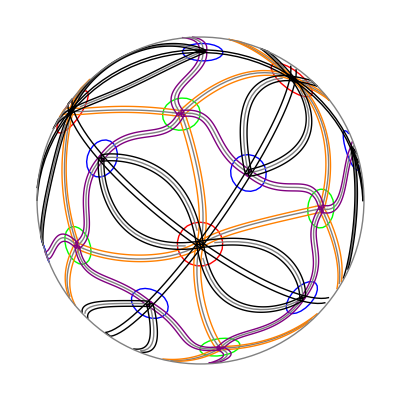

```mathematica
rradius = .09;
swdth=.012;

vview=rotz[Pi/5].rotx[Pi/10].rotx[Pi]//N;
(*vview=ident;*)

eqwidth=.025;

thegroup = "3*2";

ggg=#.vview&/@Subscript[G, thegroup]//N;

Graphics[
{(*(flatLine/@(Join @@ ((# ⊗ ggg)&/@#)))&@whiteout,*)
{Red,flatLine[spheredisk[#,.16]]&/@
((#.vview)&/@
(Join@@({cc[[1]] }⊗ (rot3⊙{ℐ,-ℐ}))))},
{Blue,flatLine[spheredisk[#,.13]]&/@
((#.vview)&/@
(Join@@({cc[[2]] }⊗ (rot3⊙{ℐ,rotz[Pi]}⊙{ℐ,rotx[Pi]}))))},
{Green,flatLine[spheredisk[#,.13]]&/@
((#.vview)&/@
(Join@@({cc[[3]] }⊗ (rot4⊙{ℐ,-ℐ}))))},

{LightGreen,flatLine[spheredisk[#,.06]]&/@
((#.vview)&/@
(Join@@({cc[[3]] }⊗ (rot4⊙{ℐ,-ℐ}))))},
{{Gray,(flatLine/@(Table[#/√(#.#)&@(#/.{t->tt}),{t,0,1,.05}]⊗ ggg))&@
spline[  cc⟦1⟧,cc⟦3⟧,{.4,1,0},{0,0,0}]
},
{Orange,flatLine/@((ffattenby[spline[  cc⟦1⟧,cc⟦3⟧,OverBar[{.4,1,0}],{0,0,0}],2 swdth]⊗ ggg))}
},
{{Gray,(flatLine/@(Table[#/√(#.#)&@(#/.{t->tt}),{t,0,1,.05}]⊗ ggg))&@
#
},
{Purple,flatLine/@((ffattenby[#,2 swdth]⊗ ggg))}
}&@spline[  cc⟦3⟧,cc⟦2⟧,.6{-1,1,0},{1,-.1,0}],


{{Gray,(flatLine/@(Table[#/√(#.#)&@(#/.{t->tt}),{t,0,1,.05}]⊗ ggg))&@
#
},
{Black,flatLine/@((ffattenby[#,2 swdth]⊗ ggg))}
}&@spline[  cc⟦1⟧,cc⟦5⟧,1.5{1,1,0},.1{-1,1,0}],


(*,
flatLine[spheredisk[#,rradius]]&/@(Join@@(cc[[{1,3,2}]] ⊗ ggg)),*)
	
flatLine/@(points2),
			{GrayLevel[.5],Circle[{0,0},1]}}
		,AspectRatio->Automatic]
```

```mathematica
rradius = .09;
swdth=.012;

vview=rotz[Pi/5].rotx[Pi/10].rotx[Pi]//N;
(*vview=ident;*)

eqwidth=.025;

thegroup = "3*2";

ggg=#.vview&/@Subscript[G, thegroup]//N;

Graphics3D[
{(*(flatLine/@(Join @@ ((# ⊗ ggg)&/@#)))&@whiteout,*)
{Red,Line[spheredisk[#,.16]]&/@
((#.vview)&/@
(Join@@({cc[[1]] }⊗ (rot3⊙{ℐ,-ℐ}))))},
{Blue,Line[spheredisk[#,.13]]&/@
((#.vview)&/@
(Join@@({cc[[2]] }⊗ (rot3⊙{ℐ,rotz[Pi]}⊙{ℐ,rotx[Pi]}))))},
{Green,Line[spheredisk[#,.13]]&/@
((#.vview)&/@
(Join@@({cc[[3]] }⊗ (rot4⊙{ℐ,-ℐ}))))},

{LightGreen,Polygon[spheredisk[#,.06]]&/@
((#.vview)&/@
(Join@@({cc[[3]] }⊗ (rot4⊙{ℐ,-ℐ}))))},
Line/@(points2),
			



{{Gray,(Line/@(Table[#/√(#.#)&@(#/.{t->tt}),{tt,0,1,.05}]⊗ ggg))&@
spline[  cc⟦1⟧,cc⟦3⟧,{.4,1,0},{0,0,0}]
},
{Orange,Line/@((ffattenby[spline[  cc⟦1⟧,cc⟦3⟧,OverBar[{.4,1,0}],{0,0,0}],2 swdth]⊗ ggg))}
},


{{Gray,(Line/@(Table[#/√(#.#)&@(#/.{t->tt}),{tt,0,1,.05}]⊗ ggg))&@
#
},
{Purple,Line/@((ffattenby[#,2 swdth]⊗ ggg))}
}&@spline[  cc⟦3⟧,cc⟦2⟧,.6{-1,1,0},{1,-.1,0}],


{{Gray,(Line/@(Table[#/√(#.#)&@(#/.{t->tt}),{tt,0,1,.05}]⊗ ggg))&@
#
},
{Black,Line/@((ffattenby[#,2 swdth]⊗ ggg))}
}&@spline[  cc⟦1⟧,cc⟦5⟧,1.5{1,1,0},.1{-1,1,0}]


}


		,Lighting->"Neutral",AspectRatio->Automatic,Boxed->False]
```

-Graphics3D-

#### 432 tiling

```mathematica
Subscript[c, "432"]={{0,0,1},OverBar[{1,0,1}],OverBar[{1,1,1}]};
```

```mathematica
cc=Append[#,OverBar[Plus @@ #]]&[Subscript[c, "432"]]
```

{{0,0,1},{0.707107,0.,0.707107},{0.57735,0.57735,0.57735},{0.478625,0.215137,0.851254}}

```mathematica
(*cook up a list of splines *)
ss=#/√(#.#)&/@{
			spline[  cc⟦1⟧,cc⟦4⟧,0 .6{0,0,0},{0,0,0}],
			spline[  cc⟦2⟧,cc⟦4⟧,.6{0,0,0},{0,0,0}],
			spline[  cc⟦3⟧,cc⟦4⟧,0 1.2{0,0,0},{0,0,0}]
	};

(*make that into a list of lists of points *)
pp=Table[#,{t,0,1,.05}]&/@ss;
```

```mathematica
(*simple orthogonal projection of a list of points, wrapped in a Line*)
```

```mathematica
flatLine[vp_]:=(xxx=Select[vp,#[[3]]>=0&]; If[xxx==={},{}, Line[Drop[#,-1]&/@xxx]])
```

```mathematica
flatLineMinus[vp_]:=(xxx=Select[vp,#[[3]]<=0&]; If[xxx==={},{}, Line[Drop[#,-1]&/@xxx]])
```

```mathematica
vview=rotz[Pi/5].rotx[Pi/10].rotx[Pi];
```

```mathematica
ggg=#.vview&/@Subscript[G, "432"];
```

```mathematica
newcurve=Table[.05 {Sin[u],Cos[u]}//N,{u,0,2Pi,Pi/20}];
```

```mathematica
p1= OverBar[Append[#,1]] &/@newcurve;
p2=#.rotx[Pi/4]&/@p1;
p3=#.rotx[ArcTan[√2//N]].rotz[Pi/4]&/@p1;
```

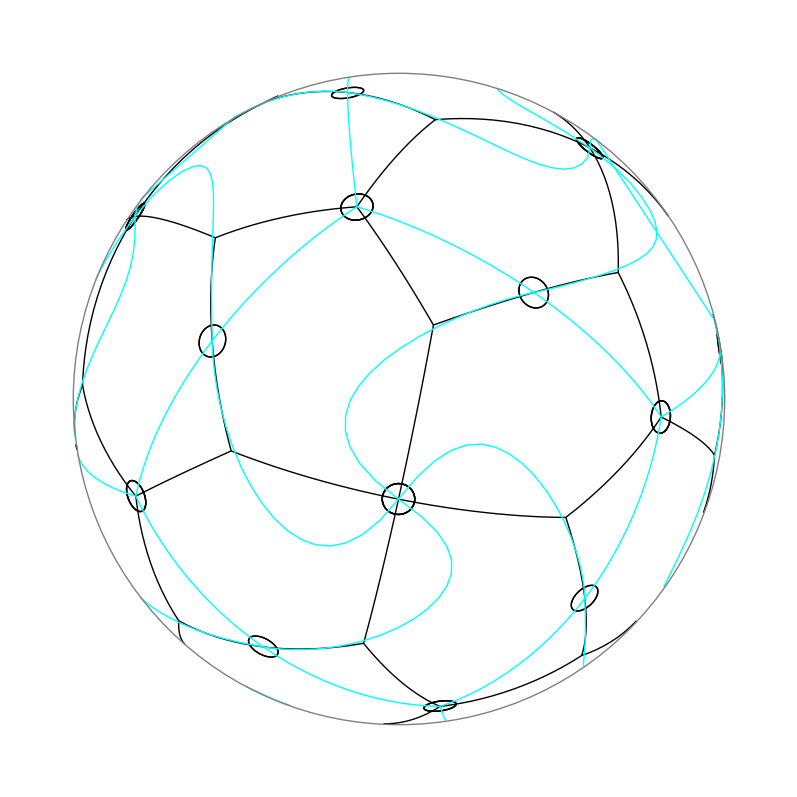

```mathematica
(*another list of splines *)
st=#/√(#.#)&/@{spline[  cc⟦1⟧,cc⟦2⟧,2{0,1,0},{0,0,0}],
			spline[  cc⟦2⟧,cc⟦3⟧,.6{0,0,0},{0,0,0}]
			(*.spline[  cc⟦3⟧,cc⟦1⟧, 1.2{0,0,0},{0,0,0}]*)
	};
ps=Table[#/.{t->tt},{tt,0,1,.05}]&/@st;(*another list of lists of points *)
Show[
	Graphics[
		Join[ 
			flatLine /@(Join @@((# ⊗ ggg)&/@pp)),
			flatLine /@(Join @@((# ⊗ ggg)&/@{p1,p2,p3})),
		{Hue[.3],PointSize[.04]},
			
			{Hue[.5]},
				flatLine /@(Join @@((# ⊗ ggg)&/@ps)),
			{GrayLevel[.5],Circle[{0,0},1]}
		

				],AspectRatio->Automatic]]
```

```mathematica
ggg=Subscript[G, "432"];
```

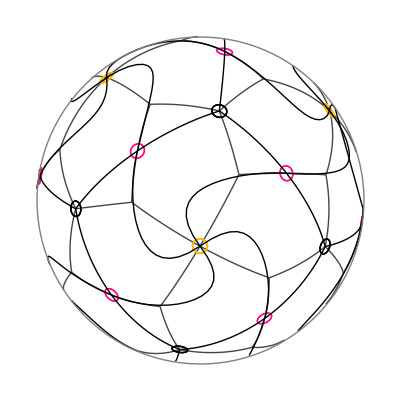
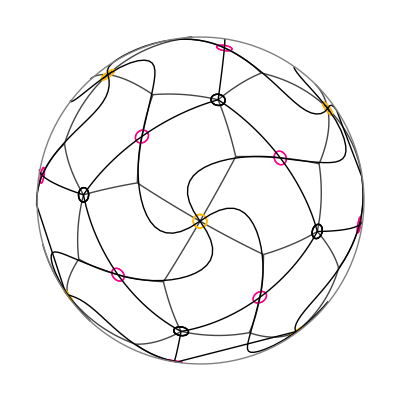
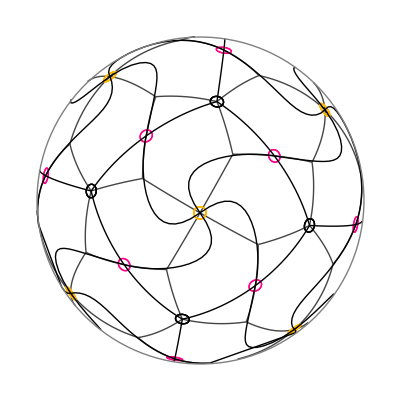
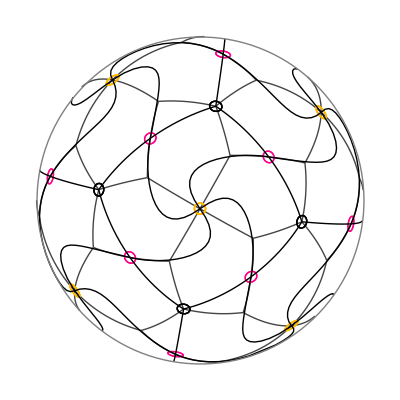
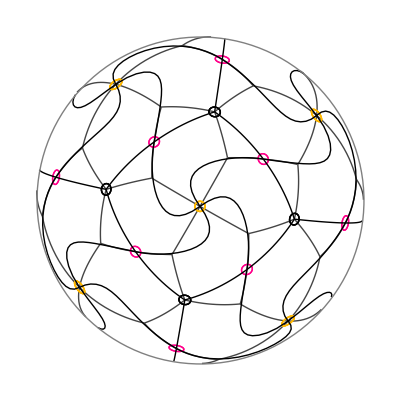
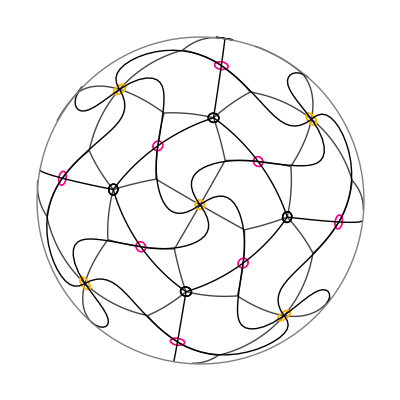
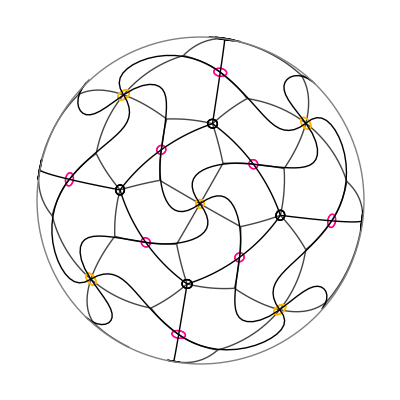
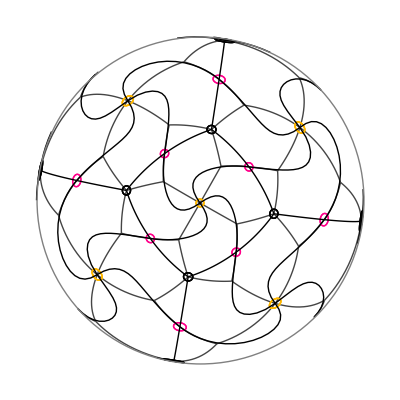

```mathematica
Table[
	
	vview=rotz[Pi/5].MatrixPower[rotx[Pi/10]
			
			
			
			
			(*rotx[Pi/10].rotx[Pi]*)
			
			
			,1./kk]//Chop[#,10^-7]&;
	ggg=#.vview&/@Subscript[G, "432"];
	
	
	Show[
	Graphics[sccaling=1.1^kk;
		Join[ 
				{GrayLevel[.27]},
	flatLine /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@pp),{2}])//Chop[#,10^-7]&,
			{Hue[.12]},
		flatLine /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@{p1}),{2}])//Chop[#,10^-7]&,
		{Hue[.91],PointSize[.04]},
					flatLine /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@{p2}),{2}])//Chop[#,10^-7]&,
				
				
		{GrayLevel[0]},
					flatLine /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@{p3}),{2}])//Chop[#,10^-7]&,
			
			{GrayLevel[0]},
					flatLine /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@ps),{2}])//Chop[#,10^-7]&,
			{GrayLevel[.5],Circle[{0,0},1]}
				],AspectRatio->Automatic]],{kk,1,17,1}]
```

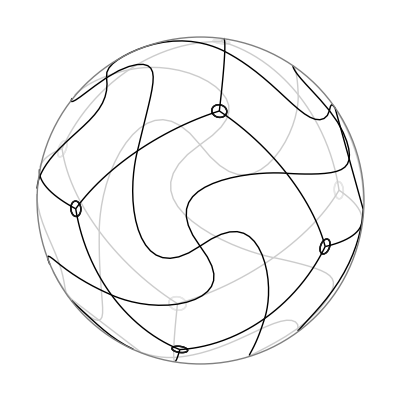
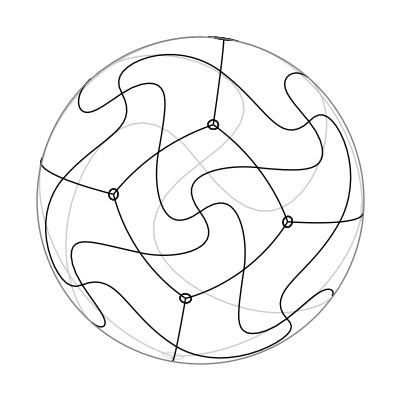
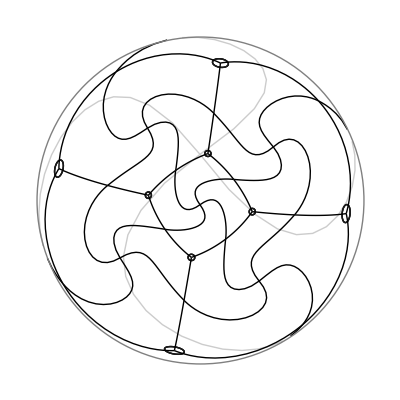

```mathematica
(kk=#;
	vview=rotz[Pi/5].MatrixPower[rotx[Pi/10]
	,1./√kk]//Chop[#,10^-7]&;
	ggg=#.vview&/@Subscript[G, "432"];
	
	
	Show[
	Graphics[sccaling=1.1^kk;
		Join[ 
	
					{GrayLevel[0.9]},
					flatLineMinus /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@{p3}),{2}])//Chop[#,10^-7]&,
			
			{GrayLevel[0.8]},
					flatLineMinus /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@ps),{2}])//Chop[#,10^-7]&,
				
				
		{GrayLevel[0.1]},
					flatLine /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@{p3}),{2}])//Chop[#,10^-7]&,
			
			{GrayLevel[0]},
					flatLine /@(Map[stereo2sphere[sccaling*stereo[#]]&,Join @@((# ⊗ ggg)&/@ps),{2}])//Chop[#,10^-7]&,
			{GrayLevel[.5],Circle[{0,0},1]}
				],AspectRatio->Automatic]])&/@{1,6,12}
```

```mathematica
ppoly=Join[
		pp⟦1⟧,
		Reverse[pp[[3]]],
		#. rot4⟦2⟧.rot3⟦-1⟧.rot5⟦5⟧           &/@ pp⟦3⟧,
		#. rot5⟦5⟧.rot4⟦3⟧         &/@ Reverse[pp⟦2⟧],
		#.rot4⟦3⟧         &/@ pp⟦2⟧,
		#.rot4⟦3⟧         &/@ Reverse[pp⟦1⟧]
	
	
	];
```

```mathematica
Show[Graphics3D[Join[{Line[ppoly],Hue[.3],PointSize[.04]},Point /@ cc],ViewPoint->10{0,0,1},Boxed->False],mask,DisplayFunction->$DisplayFunction,Lighting->False]
```

-Graphics3D-

### other projections

```mathematica
swirl=sswirl[3,2.3,100,rot[-Pi/6].scale[.4].trans[{.050,0}]];

sphswirl=pl2sp /@ (homo2cart /@ swirl);
sphpoly:=sphswirl
```

```mathematica
Table[Show[Graphics[
		
		
		
		
		Line /@ (
						stereo ⋆(	(sphpoly .#) & /@  (Subscript[G, "532"]⊙{rotx[.010121].roty[Pi/40 k]}//N)))
								
				
	
			
			
			
			,AspectRatio->Automatic,PlotRange->3{{-1,1},{-1,1}},Axes->False]],{k,0,39}]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

```mathematica
Table[Show[Graphics[
		
		
		
		
		Line /@ (homo2cart ⋆  (Join @@
						(abovelist[#,{0,0,1},Identity]&/@((	(sphpoly .#) & /@  (Subscript[G, "532"]⊙{rotx[.010121].roty[Pi/40 k]}//N))))))
								
				
	
			
			
			
			,AspectRatio->Automatic,PlotRange->5{{-1,1},{-1,1}},Axes->False]],{k,1,1}]
```

{⁃Graphics⁃}

```mathematica
Table[Show[Graphics[
		
		
		
		
		Line /@ (homo2cart ⋆ (Join @@ 
								(abovelist[#,{1,0,4},Identity]& /@ (Join @@
						(abovelist[#,{0,0,1},Identity]&/@((	(sphpoly .#) & /@  (Subscript[G, "532"]⊙{rotx[.010121].roty[Pi/40 k]}//N))))))))
								
				
	
			
			
			
			,AspectRatio->Automatic,PlotRange->5{{-1,1},{-1,1}},Axes->False]],{k,1,1}]
```

{⁃Graphics⁃}

```mathematica
abovelist[sss[[45]],{1,2,1},#&]
```

{{{-0.784648,0.328969,0.525459},{-0.784292,0.339794,0.519063},{-0.782566,0.351263,0.514009},{-0.779495,0.363146,0.510404},{-0.775128,0.375205,0.508329},{-0.76953,0.387203,0.507836},{-0.762789,0.398904,0.508949},{-0.755006,0.410082,0.511662},{-0.746298,0.420526,0.515943},{-0.736791,0.430039,0.521733},{-0.726623,0.438446,0.528946},{-0.715932,0.445598,0.537479},{-0.704864,0.451367,0.547206},{-0.693561,0.455657,0.557987},{-0.682162,0.458399,0.569671},{-0.6708,0.459553,0.582099},{-0.659599,0.459106,0.595105},{-0.648675,0.457073,0.608527},{-0.63813,0.453495,0.6222},{-0.628053,0.448435,0.635969},{-0.618517,0.441979,0.649685},{-0.609585,0.43423,0.663213},{-0.6013,0.425306,0.676427},{-0.593694,0.415338,0.689218},{-0.586782,0.404467,0.701494},{-0.580568,0.392839,0.713175},{-0.575043,0.380604,0.7242},{-0.570185,0.367915,0.734525},{-0.565965,0.35492,0.744121},{-0.562342,0.341768,0.752971},{-0.559272,0.328599,0.761077},{-0.556701,0.315551,0.768448},{-0.554574,0.30275,0.775107},{-0.552832,0.290317,0.781084},{-0.551413,0.278364,0.78642},{-0.550259,0.266992,0.791158},{-0.549307,0.256295,0.795346},{-0.5485,0.246357,0.799034},{-0.547783,0.237254,0.802274},{-0.547103,0.229055,0.805116},{-0.546413,0.221818,0.807607},{-0.54567,0.215598,0.809791},{-0.544836,0.210441,0.811707},{-0.543881,0.206388,0.813387},{-0.542777,0.203475,0.814856},{-0.541508,0.20173,0.816133},{-0.540062,0.20118,0.817227},{-0.538433,0.201845,0.818137},{-0.536624,0.20374,0.818856},{-0.534646,0.206874,0.819363},{-0.532518,0.211253,0.819632},{-0.530264,0.216876,0.819625},{-0.527919,0.223734,0.819295},{-0.525524,0.231811,0.818589},{-0.523127,0.241084,0.817445},{-0.520787,0.25152,0.815793},{-0.518566,0.263072,0.813562},{-0.516534,0.275687,0.810672},{-0.514767,0.289295,0.807046},{-0.513347,0.303813,0.802603},{-0.51236,0.319145,0.797267},{-0.511893,0.335176,0.790963},{-0.512036,0.351779,0.783626},{-0.512879,0.36881,0.775199},{-0.51451,0.386107,0.765638},{-0.517012,0.403495,0.754911},{-0.520462,0.420787,0.743006},{-0.524929,0.437779,0.729931},{-0.530471,0.454263,0.715714},{-0.537131,0.47002,0.700408},{-0.544938,0.484829,0.684093},{-0.553903,0.498472,0.666871},{-0.564014,0.510734,0.648875},{-0.57524,0.52141,0.630262},{-0.587526,0.530312,0.611214},{-0.600792,0.537272,0.591936},{-0.614933,0.542149,0.572653},{-0.629823,0.544833,0.553607},{-0.645308,0.545251,0.53505},{-0.661217,0.543372,0.517242},{-0.677358,0.539207,0.500442},{-0.693525,0.532816,0.484902},{-0.7095,0.524308,0.470862},{-0.725058,0.51384,0.45854},{-0.739974,0.501617,0.448129},{-0.754025,0.487889,0.439783},{-0.767003,0.472947,0.433622},{-0.77871,0.457117,0.429714},{-0.788975,0.440753,0.428083},{-0.797654,0.424228,0.428695},{-0.804632,0.407927,0.431466},{-0.809835,0.392234,0.436256},{-0.813228,0.377525,0.442872},{-0.814816,0.364151,0.451075},{-0.81465,0.352438,0.46058},{-0.812821,0.342665,0.471065},{-0.809464,0.335067,0.482181},{-0.804749,0.329818,0.493557},{-0.798882,0.327032,0.504814},{-0.792096,0.326756,0.515571},{-0.784648,0.328969,0.525459}}}

Preparing A File for Symagary

### The Groups

```mathematica
sphericalgps = {"222","*222","332","3*2","*332","432","*432","532","*532"}
```

{222,*222,332,3*2,*332,432,*432,532,*532}

```mathematica
(Subscript[atr, #]="X")&/@sphericalgps
```

{X,X,X,X,X,X,X,X,X}

We'll add these soon: ,"*532","55","*55","225","5x","5*","2*5","*225", etc. These will be atr = Y is flexible, Z if not.

G_("nn",5);G_("*nn",5);G_("22n",5);G_("nx",5);G_("n*",5);G_("2*n",5);G_("*22n",5);

```mathematica
(Subscript[mirlines, #]={})& /@ sphericalgps;
(rotpts[2][#]={})&/@sphericalgps;
(rotpts[3][#]={})&/@sphericalgps;
(rotpts[4][#]={})&/@sphericalgps;
(rotpts[5][#]={})&/@sphericalgps;
```

#### 222

```mathematica
rotpts[2]["222"]={0,0,1}.#&/@{ident,refz}⊙rot3;
```

```mathematica
Subscript[fund, "222"]={{1,0,0},{0,0,-1},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,0,-1},{0,1,0},{0,0,1}}

#### *222

```mathematica
Subscript[mirlines, "*222"]={1,0,0}.#&/@rot3;
```

```mathematica
Subscript[fund, "*222"]={1,0,0}.#&/@rot3;
```

fundlines_("*222")=mirlines_("*222");

#### 332

```mathematica
rotpts[2]["332"]=rotpts[2]["222"];
rotpts[3]["332"]=OverBar[{1,1,1}].#&/@ Subscript[G, "*222"];
```

fundlines_("332")=OverBar[#]&/@ {{-1,1,0},{-1,0,-1},{-1,-1,0},{-1,0,1}};

```mathematica
Subscript[fund, "332"]=OverBar[#]&/@{{1,1,1},{0,1,0},{-1,1,1},{0,0,1}};
```

#### 3*2

```mathematica
rotpts[3]["3*2"]=rotpts[3]["332"];
```

```mathematica
Subscript[mirlines, "3*2"]=Subscript[mirlines, "*222"];
```

```mathematica
Subscript[fund, "3*2"]={{0,0,1},OverBar[{1,1,1}],{0,1,0}};
```

#### *332

```mathematica
Subscript[fund, "*332"]={{1,1,1},{-1,1,1},{0,0,1}};
```

```mathematica
Subscript[mirlines, "*332"]=OverBar[#]&/@{{1,1,0},{1,-1,0},{0,1,1},{0,1,-1},{1,0,1},{1,0,-1}};
```

#### 432

```mathematica
Subscript[fund, "432"]=Subscript[fund, "*332"];
```

```mathematica
rotpts[4]["432"]=rotpts[2]["222"];
rotpts[3]["432"]=rotpts[3]["332"];
```

```mathematica
rotpts[2]["432"]=OverBar[{1,1,0}.#]&/@ Subscript[G, "332"];
```

#### *432

```mathematica
Subscript[fund, "*432"]={{1,1,1},{0,1,1},{0,0,1}};
```

```mathematica
Subscript[mirlines, "*432"]=Join[Subscript[mirlines, "*222"],Subscript[mirlines, "*332"]];
```

#### 532

```mathematica
Subscript[fund, "532"]=OverBar[N[#]]&/@ {{1,0,ϕ},{ϕ,1,0},{1,1,1}};
```

```mathematica
rotpts[2]["532"]=OverBar[{1,0,0}.#]&/@ ({ident,refz}⊙rot3⊙rot5);
```

```mathematica
rotpts[3]["532"]=OverBar[{1,1,1}.#]&/@Join[({rot5[[2]]}⊙Subscript[refz, 2]⊙(Subscript[refx, 2]⊙rot3))//N,Subscript[G, "*222"]];
```

```mathematica
rotpts[5]["532"]=OverBar[{1,0,ϕ}.#]&/@(Subscript[refx, 2]⊙Subscript[refz, 2]⊙rot3)//N;
```

#### *532

```mathematica
Subscript[fund, "*532"]=OverBar[N[#]]&/@ {{1,0,ϕ},{ϕ+1,1,ϕ},{1,1,1}};
```

```mathematica
Subscript[mirlines, "*532"]=OverBar[N[#]]&/@(Subscript[mirlines, "*222"]⊙rot5)
```

{{1.,0,0},{0.5,-0.809017,0.309017},{-0.309017,-0.5,0.809017},{-0.309017,0.5,0.809017},{0.5,0.809017,0.309017},{0,1.,0},{0.809017,0.309017,-0.5},{0.5,-0.809017,-0.309017},{-0.5,-0.809017,0.309017},{-0.809017,0.309017,0.5},{0,0,1.},{0.309017,0.5,0.809017},{0.809017,0.309017,0.5},{0.809017,-0.309017,0.5},{0.309017,-0.5,0.809017}}

### Writing them out:

```mathematica
commentQ=False;
```

```mathematica
file="Sally:Desktop Folder:SphericalSymmetries.txt"
```

Sally:Desktop Folder:SphericalSymmetries.txt

```mathematica
OpenWrite[file]
```

OutputStream[Sally:Desktop Folder:SphericalSymmetries.txt,4]

```mathematica
matwrite[file_,matr_]:=
	(Table[
				WriteString[file,Sequence @@ (Join @@ Table[{ToString[OutputForm[PaddedForm[matr⟦i,j⟧//N,{8,6}]]],"    "},{j,1,3}])];
				
		WriteString[file,"\n"],{i,1,3}];WriteString[file,"\n"])
```

```mathematica
sp="    ";
```

```mathematica
numwrite[n_]:=ToString[OutputForm[PaddedForm[n//N,{8,6}]]]
```

```mathematica
Sgpwrite[file_,name_]:=
	
(
	
	
	WriteString[file,
			
			
			
			If[commentQ,"\n################",""]<>
				
					"\n \n"<> name<>
					"    "<> ToString[Subscript[atr, name]]<>"\n\n"];
					
					
		WriteString[file,	
				If[commentQ,	"# the fund region\n",""]<>
					ToString[Length[Subscript[fund, name]]]<>"\n"];
					
			Table[WriteString[file,numwrite[Subscript[fund, name]⟦i,1⟧]<>sp<>numwrite[Subscript[fund, name]⟦i,2⟧]<>sp<>numwrite[Subscript[fund, name]⟦i,3⟧]<>"\n"],
				{i,1,Length[Subscript[fund, name]]}];WriteString[file,"\n\n"];
		
	 If[commentQ,WriteString[file,"# the mirror lines and rotation points\n"]];			
	
		WriteString[file,ToString[Length[Subscript[mirlines, name]]]<>"\n"];
		i=0; While[i<Length[Subscript[mirlines, name]],i++;
			WriteString[file,numwrite[Subscript[mirlines, name][[i,1]]]<>"   "<>
					numwrite[Subscript[mirlines, name][[i,2]]]<>sp<>numwrite[Subscript[mirlines, name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];
	
				WriteString[file,ToString[Length[rotpts[2][name]]]<>"\n"];
				i=0; While[i<Length[rotpts[2][name]],i++;
			WriteString[file,
					numwrite[rotpts[2][name][[i,1]]]<>sp<>numwrite[rotpts[2][name][[i,2]]]<>sp<>numwrite[rotpts[2][name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];			
		
			WriteString[file,ToString[Length[rotpts[3][name]]]<>"\n"];
		i=0; While[i<Length[rotpts[3][name]],i++;
			WriteString[file,
					numwrite[rotpts[3][name][[i,1]]]<>sp<>numwrite[rotpts[3][name][[i,2]]]<>sp<>numwrite[rotpts[3][name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];			
					
			WriteString[file,ToString[Length[rotpts[4][name]]]<>"\n"];
		i=0; While[i<Length[rotpts[4][name]],i++;
			WriteString[file,
					numwrite[rotpts[4][name][[i,1]]]<>sp<>numwrite[rotpts[4][name][[i,2]]]<>sp<>numwrite[rotpts[4][name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];			
				
				WriteString[file,ToString[Length[rotpts[5][name]]]<>"\n"];	
		i=0; While[i<Length[rotpts[5][name]],i++;
			WriteString[file,
					numwrite[rotpts[5][name][[i,1]]]<>sp<>numwrite[rotpts[5][name][[i,2]]]<>sp<>numwrite[rotpts[5][name][[i,3]]]<>"\n"]];
		
					If[commentQ,WriteString[file,"\n\n# the transforms\n"]];	
			WriteString[file,
				"\n"<>ToString[Length[Subscript[G, name]]]<>sp<>
			"\n\n"];
				Table[matwrite[file,Subscript[G, name]⟦i⟧],{i,1,Length[Subscript[G, name]]}];
	WriteString[file,"\n\n"]
			
			)
```

```mathematica
WriteString[file, ToString[Length[sphericalgps]]<>"\n"];

Sgpwrite[file,#]&/@sphericalgps;Close[file]
```

Sally:Desktop Folder:SphericalSymmetries.txt